# RF Modulation Sweep (Frequency) - Photon Correlation Counts

## Last Updated: 03/29/2022

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-03-28";
(*directoryString="C:\\Users\\EGGS2\\Documents\\datatmp_rf";*)
```

```mathematica
(*select runs*)
ridList={15354};
```

## Setup

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Sided Conversion

```mathematica
(*convert double-sided to single-sided*)
GetSingleSidedX[data_List]:=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]];
```

```mathematica
GetSingleSidedY[data_List]:=With[
{trimmedData=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]]},
Return[(2*#1-UnitVector[#2,1]*#1[[1]])&[trimmedData,Length[trimmedData]]]
];
```

### Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut;

(*return dataset*)
Return[results];
]
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
results=Transpose[
{datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,2]],datasetRaw[[;;,3]]}
];

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

## Import

## Import File

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString/@ridList]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

## Extract Values

```mathematica
(*import and process data*)
dataset=ProcessDatasetCounts[filenameDJ];
(*sort dataset*)
dataset=SortBy[dataset,First];
```

```mathematica
(*get parameters*)
modulationAmplitude=Import[filenameDJ,{"/datasets/modulation_amplitude_vpp"}];
shimVoltage=Import[filenameDJ,{"/datasets/dc_channel_voltage"}];
```

## Plot

## Fit Phase

```mathematica
(*process phase data for fitting*)
rawPhaseData=dataset[[;;,{1,4}]];
processedPhaseData=Transpose[{dataset[[;;,1]],Tan[dataset[[;;,4]]]}];
```

```mathematica
(*create phase model*)
phaseModel=ArcTan[α*x/(x^2-β^2)+γ]+δ;
phaseConstraints={(*α>0,β>0,Abs[γ]<π/2*)};
```

```mathematica
(*fit phase & get fit functions*)
phaseFit=FindFit[rawPhaseData,Join[{phaseModel,phaseConstraints}],{α,β,γ,δ},x,MaxIterations->100000]
rawPhaseFunction=phaseModel/.{γ->0}/.phaseFit;
processedPhaseFunction=Tan[rawPhaseFunction];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{α→-9.88881×10^6,β→-114.906,γ→-902.414,δ→0.592685}

```mathematica
(*create raw phase figures*)
{rawPhasePlot,fittedRawPhasePlot}={
ListLinePlot[
{dataset[[;;,{1,4}]]},
PlotRange->Full
],
Plot[
rawPhaseFunction,
{x,##}&@@rawPhaseData[[{1,-1},1]],
PlotStyle->Directive[Dashed,Orange]
]
};
```

```mathematica
(*create processed phase figures*)
{processedPhasePlot,fittedProcessedPhasePlot}={
ListLinePlot[
processedPhaseData
],
Plot[
processedPhaseFunction,
{x,##}&@@rawPhaseData[[{1,-1},1]],
PlotRange->Full,
PlotStyle->Directive[Dashed,Orange]
]
};
```

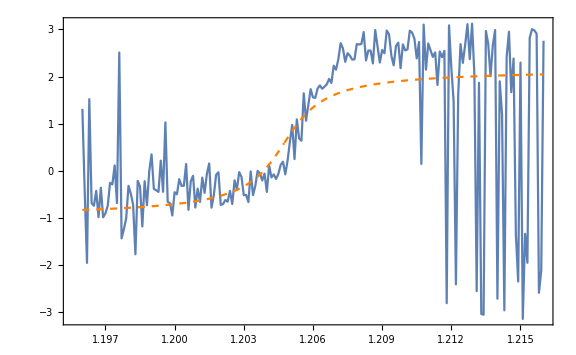
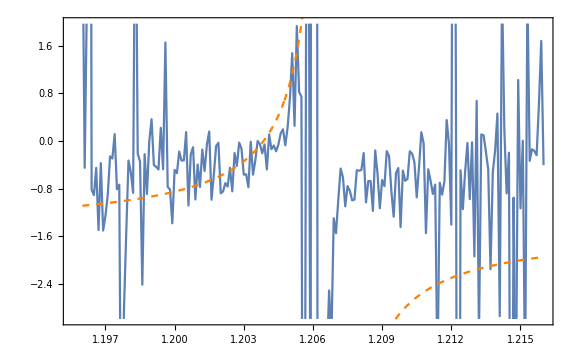

```mathematica
{
Show[rawPhasePlot,fittedRawPhasePlot],
Show[processedPhasePlot,fittedProcessedPhasePlot]
}
```

## Create Figures

```mathematica
(*amplitude plot*)
amplitudePlot=ListLinePlot[
dataset[[;;,{1,3}]],
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
];
```

```mathematica
(*phase plot*)
phasePlot=ListLinePlot[
dataset[[;;,4]]/π,
DataRange->dataset[[{1,-1},1]],
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (π rad.)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Phase - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
];
```

## Summary

Shim Voltage (V): 30.

Modulation Amplitude (V): 0.05

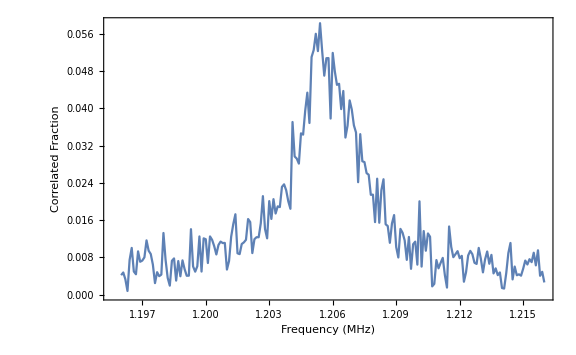
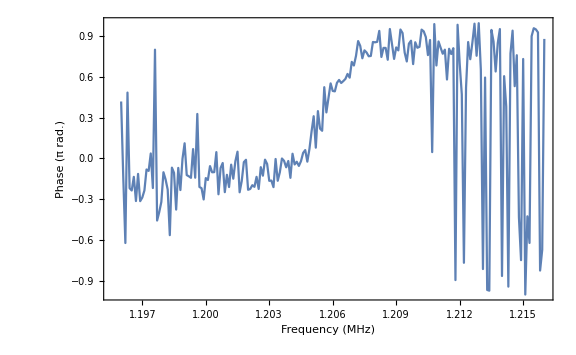

```mathematica
Print["Shim Voltage (V): "<>ToString[shimVoltage]]
Print["Modulation Amplitude (V): "<>ToString[modulationAmplitude]]
{amplitudePlot,phasePlot}
(*correlatedRatePlot*)
```

## Deprecated

## Importing

```mathematica
(*(*get parameters*)
xArr=Import[#,{"/datasets/xArr"}]*1*^6&/@filenamesDJ;
xArr=Sort/@xArr;*)
```

## Processing

```mathematica
(*get time difference in seconds*)
(*datasets=(#[[;;,3]]-#[[;;,2]])/(1*^9)&/@datafile;*)
```

```mathematica
(*get total count times*)
(*datasetTimes=N[(#[[-1,3]]-#[[1,2]])/(1*^9)]&/@datafile;*)
(*get total count rates*)
(*datasetRates=numPoints/datasetTimes;*)
```

## Fitting

### Preprocess

```mathematica
(*fitData=histData;*)
```

```mathematica
(*(*remove offset*)
(*fitData=#-Mean[#]&/@fitData[[;;,;;,2]];*)*)
```

```mathematica
(*(*fit constraints*)
fitConstraints={
0<=a<=40,
1*2*π<=b<=2*π*3,
0<=c<=2π
};*)
```

### Fitting

```mathematica
(*(*fit sine*)
AbsoluteTiming[dataFits=ParallelMap[
NonlinearModelFit[#,
Join[{a*Sin[b*x+c]+d},fitConstraints],
{a,b,c,d},x,
Method->Automatic,
MaxIterations->1000
]&,
histData
];]*)
```

```mathematica
(*(*extract parameters*)
fittedParameterTables=#["ParameterTable"][[1]]&/@dataFits;
fittedParameters=fittedParameterTables[[;;,1,2;;5,{2,3}]];
{fittedAmplitudes,fittedFrequencies,fittedPhases,fittedOffsets}=Transpose[fittedParameters];*)
```

### Plot Fit

```mathematica
(*fitSinFunc[A_,ω_,ϕ_,C_]:=A*Sin[ω*x+ϕ]+C;*)
```

```mathematica
(*(*create plot of fitted equation*)
fitSinEqns=fitSinFunc@@#&/@fittedParameters[[;;,;;,1]];
fitSinPlots=Plot[#,{x,histData[[1,1,1]],histData[[1,-1,1]]}]&/@fitSinEqns;*)
```

```mathematica
(*(*combine figures*)
combinedPlots=MapThread[Show[#1,#2]&,{histPlots,fitSinPlots}];*)
```

## Plotting

```mathematica
(*yz1=HistogramList[#,1000]&/@datasets;
mzdp1=Sqrt[GetSingleSidedY[Abs[Fourier[yz1[[1,2]]]]^2]];
ListLinePlot[%]*)
```